```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
osxdata=Flatten[Import["osx_macair_2013.csv"]];
```

```mathematica
ListPlot[osxdata]
```

-Graphics-

```mathematica
diff=Table[Subtract[osxdata⟦i⟧,osxdata⟦i-1⟧] , {i,2,Length[osxdata],1}];
```

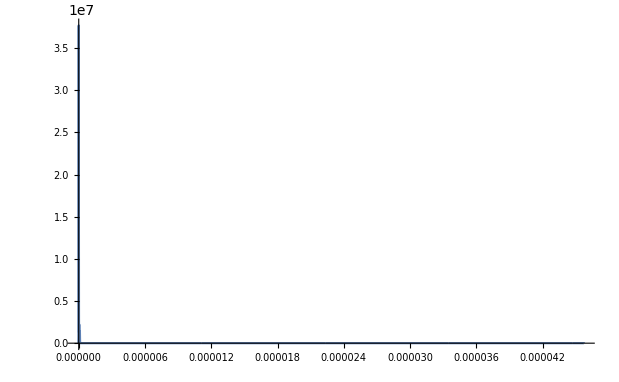

```mathematica
SmoothHistogram[diff,PlotRange->Full]
```